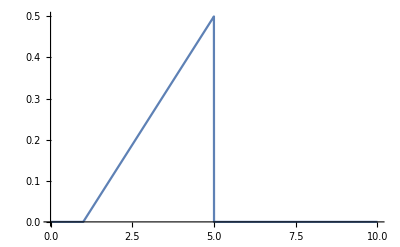

```mathematica
(*Ex 5*)
(*Subpunctul 1*) (*Varianta 4*)
f[x_]:=0/; x<1;
f[x_]:=(x-1)/8 /;1≤x≤5;
f[x_]:= 0 /; x>5;
Plot[f[x],{x,0,10}]
```

```mathematica
(*Subpunctul 3*)
∫_1^x (x-1)/8 ⅆx
```

1/16-x/8+x^2/16

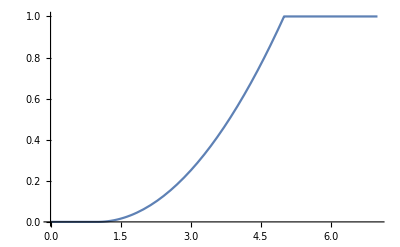

```mathematica
1/16-x/8+x^2/16

F[x_]:=0/;x<1;
F[x_]:=1/16-x/8+x^2/16/;1≤x≤5;
F[x_]:=1/;x>5;
Plot[F[x],{x,0,7}]
```

```mathematica
(*Subpunctul 12*)(*Mijlocul intervalului este 1+5/2 care e egal cu 3*)

N[ F[3]-F[1]];
```

```mathematica
0.25
```

0.25

```mathematica
(*Ex.6*)  (*Varianta 4)m=6,σ=2,α=4,β=9;*)

(*Subpunctul 1)*)
<<Statistics`NormalDistribution`


(*Subpunctul 2)*)(*Varianta 4)m=6,σ=2,α=4,β=9;*)
rn=NormalDistribution[6,2]
```

Get::noopen: Cannot open Statistics`NormalDistribution`.

$Failed

NormalDistribution[6,2]

Get::noopen: Cannot open Statistics`NormalDistribution`.

Syntax::sntxi: Incomplete expression; more input is needed .

```mathematica
(*Subpunctul 3 *)
drn=PDF[rn,x]
```

(ⅇ^(-1/8 (-6+x)^2))/(2 √(2 π))

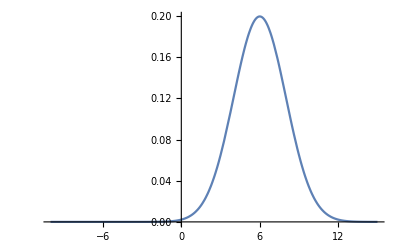

```mathematica
(ⅇ^(-1/8 (-6+x)^2))/(2 √(2 π))
Plot [drn,{x,-10,15}]
```

```mathematica
(*Subpunctul 6*)
frn=CDF[rn,x]
```

1/2 Erfc[(6-x)/(2 √2)]

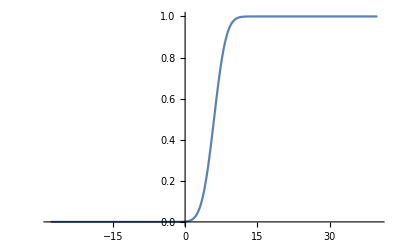

```mathematica
Plot[frn,{x,-27.941125496954278,39.94112549695428}]
```

```mathematica
(*Subpunctul 9*)
N[frn[9]-frn[4]]
```

```mathematica
-1. (0.5 Erfc[0.35355339059327373 (6.-1. x)])[4.]+(0.5 Erfc[0.35355339059327373 (6.-1. x)])[9.]

(*Ex.7*)

(*Varianta*n=4 
m=175.25 
σ=5.75*)
 F(x)=1/(σ*√(2*π))*e^(-(x-m)^2/(2*σ^2))
(*A*)
N[∫_150^155 1/(5.75*√(2π))*e^(-(x-175.25)^2/(2*5.75^2))ⅆx]
```

Set::write: Tag Times in F x is Protected.

(e^(-(-175.25+x)^2/(2 σ^2)))/(√(2 π) σ)

(-0.5 Erf[2.61322 √Log[e]]+0.5 Erf[3.10512 √Log[e]])/(√Log[e])

```mathematica
(*B*)
N[∫_155^160 1/(5.75*√(2π))*e^(-(x-175.25)^2/(2*5.75^2))ⅆx]
```

(-0.5 Erf[1.87537 √Log[e]]+0.5 Erf[2.49025 √Log[e]])/(√Log[e])

```mathematica
(*C*)
N[∫_160^165 1/(5.75*√(2π))*e^(-(x-175.25)^2/(2*5.75^2))ⅆx]
```

(-0.5 Erf[1.26049 √Log[e]]+0.5 Erf[1.87537 √Log[e]])/(√Log[e])

```mathematica
(*D*)
N[∫_165^170 1/(5.75*√(2π))*e^(-(x-175.25)^2/(2*5.75^2))ⅆx]
```

(-0.5 Erf[0.645619 √Log[e]]+0.5 Erf[1.26049 √Log[e]])/(√Log[e])

```mathematica
(*E*)
N[∫_170^175 1/(5.75*√(2π))*e^(-(x-175.25)^2/(2*5.75^2))ⅆx]
```

(-0.5 Erf[0.0307438 √Log[e]]+0.5 Erf[0.645619 √Log[e]])/(√Log[e])

```mathematica
(*F*)
```

```mathematica
N[∫_175^180 1/(5.75*√(2π))*e^(-(x-175.25)^2/(2*5.75^2))ⅆx]
```

(0.5 Erf[0.0307438 √Log[e]]+0.5 Erf[0.584132 √Log[e]])/(√Log[e])

```mathematica
(*G*)
N[∫_180^185 1/(5.75*√(2π))*e^(-(x-175.25)^2/(2*5.75^2))ⅆx]
```

(-0.5 Erf[0.584132 √Log[e]]+0.5 Erf[1.19901 √Log[e]])/(√Log[e])

```mathematica
(*H*)
N[∫_185^190 1/(5.75*√(2π))*e^(-(x-175.25)^2/(2*5.75^2))ⅆx]
```

(-0.5 Erf[1.19901 √Log[e]]+0.5 Erf[1.81388 √Log[e]])/(√Log[e])

```mathematica
(*I*)
N[∫_190^195 1/(5.75*√(2π))*e^(-(x-175.25)^2/(2*5.75^2))ⅆx]
```

(-0.5 Erf[1.81388 √Log[e]]+0.5 Erf[2.42876 √Log[e]])/(√Log[e])

```mathematica
(*J*)
N[∫_195^200 1/(5.75*√(2π))*e^(-(x-175.25)^2/(2*5.75^2))ⅆx]
```

(-0.5 Erf[2.42876 √Log[e]]+0.5 Erf[3.04363 √Log[e]])/(√Log[e])

```mathematica
(*EX.8 *)
(*1)*)
f[x_]:=5*e^(-5x)/;x≥0; (*densitatea de repartitie*)
f[x_]= 0/;x<0;
Plot[f[x],{x,-4,6}]
```

-Graphics-

```mathematica
(*2)*)
F[x_]:=1-e^(-5x)/;x>0;
F[x_]=0/;x≤0;
Plot[F[x_],{x, -4,8}]
```

-Graphics-

```mathematica
(*3)*)
P=N[e^(-(2+4/3)5)]
```

```mathematica
1/e^(50/3)

(*Ex.9*)(*1)*)
F[x_]:=0/;x<0;F[x_]:=1/30/;0≤x≤30;F[x_]:=1/;x>30;
```

```mathematica
(*2)*)
```

```mathematica
Plot[F[x],{x,-4,10}]
```

-Graphics-

```mathematica
(*4)*) (*10+n/2=12 deoarece n=4*)
N[∫_0^12 1/30 ⅆx]
```

```mathematica
0.4
```

0.4

```mathematica
(*EX.10*)
(*1*)
F[x]=1/(150 √(2π))e^(-(x-500)^2/(2*150)^2)

(*2)*)
N[∫_420^520 1/(150*√(2*π))e^(-(x-500)^2/(2*150)^2)ⅆx]
```

(e^(-(-500+x)^2/90000))/(150 √(2 π))

(0.707107 (Erf[0.0666667 √Log[e]]+Erf[0.266667 √Log[e]]))/(√Log[e])

```mathematica
(*3*)
N[∫_0^300 1/(150*√(2*π))e^(-(x-500)^2/(2*150)^2)ⅆx]
```

(0.707107 (-1. Erf[0.666667 √Log[e]]+Erf[1.66667 √Log[e]]))/(√Log[e])